# Vaje 4

13. 3. 2025

## 1. kolokvij iz Matematike 1

1. Dokaži, da je za vsako naravno število  izraz  deljiv s .

```mathematica
izraz = Power[2, 2 * n +1] - 9 n * n+ 3 n - 2
```

-2+2^(1+2 n)+3 n-9 n^2

```mathematica
(* Baza indukcije *)
izraz /. {n -> 1}
```

0

```mathematica
(* 27 deli 0*)
```

```mathematica
(* Indukcijski korak *)
```

```mathematica
izrazKorak = izraz /. {n ->  m + 1}
```

-2+2^(1+2 (1+m))+3 (1+m)-9 (1+m)^2

```mathematica
ostanek = (izrazKorak - (izraz /. {n -> m})) // FullSimplify
```

6 (-1+4^m-3 m)

```mathematica
(* To je deljvivo s 6, zato tudi s 3, pokažemo da je oklepaj deljiv z 9 *)
```

```mathematica
indukcija2izraz = ostanek /6
```

-1+4^m-3 m

```mathematica
(* baza *)
indukcija2izraz /. {m -> 1}
```

0

```mathematica
(* korak *)
indukcija2izrazKorak = indukcija2izraz /. {m -> k + 1}
```

-1+4^(1+k)-3 (1+k)

```mathematica
ostanek2 = (indukcija2izrazKorak - (indukcija2izraz /. {m -> k})) // FullSimplify
```

3 (-1+4^k)

```mathematica
(* Isti postopek še da dobimo da 3 | (4^k - 1) *)
```

2.  Določi vsa realna števila , ki zadoščajo neenačbi .

```mathematica
Reduce[Abs[x * x + 3x+2] + Abs[x + 2] > 2x*x + x]
```

-1<x<4

3. V kompleksnih številih reši enačbo . Rešitve nariši v kompleksni ravnini.

```mathematica
solutions = Solve[Power[z, 6] + 2I * Power[z, 3] + 3 == 0, {z}]
```

{{z→-ⅈ},{z→ⅈ 3^(1/3)},{z→-(-1)^(1/6) 3^(1/3)},{z→-(-1)^(5/6) 3^(1/3)},{z→1/2 (ⅈ-√3)},{z→1/2 (ⅈ+√3)}}

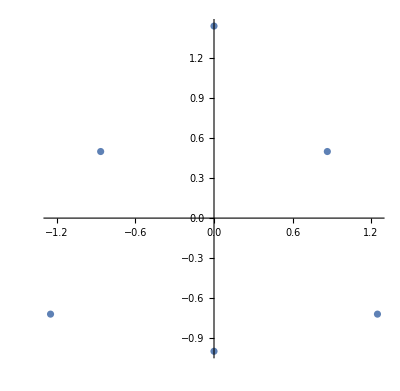

```mathematica
ComplexListPlot[(Flatten[solutions] // Values)]
```

4. Dana je množica . Ugotovi, katere od količin min A, inf A, max A in sup A obstajajo ter jih določi. Vse odgovore natančno utemelji.

```mathematica
(* Izračunamo minimum in maximum funkcije, nato preverimo, če je vrednost kje dejansko dosežena *)
f[n_] := (8n+2)/(4n-1)
```

```mathematica
D[f[n], n] // Simplify
```

-16/(1-4 n)^2

```mathematica
(* Odvod je manjši od 0, funkcija torej pada proti limiti. Alternativno lahko pogledamo razliko zaporednih členov. *)
```

```mathematica
f[n] - f[n + 1] // FullSimplify
```

16/(-3+8 n+16 n^2)

```mathematica
Limit[f[x], x -> Infinity]
```

2

```mathematica
f[1]
```

10/3

```mathematica
Solve[f[n] == 2, {n}]
```

{}

```mathematica
(* Sledi torej max = sup = 10/3, min ne obstaja, inf = 2 *)
```

## 2. kolokvij iz Matematike 1

1. Funkcija  je podana s predpisom

 
Izračunaj naravno definicijsko območje funkcije  in izračunaj kompozitum , kjer je 

g funkcija, ki je za  enaka , sicer pa je enaka .

```mathematica
f[x_] := Log[ArcSin[(3 + x) / (3x -1)]]
```

```mathematica
FunctionDomain[f[x], x]
```

x<-3||x≥2

```mathematica
g[x_] := Piecewise[{{E^x, x <= Log[Pi/2]}, {E^(-x), x > Log[Pi/2]}}]
```

```mathematica
g[f[y]] // FullSimplify
```

Piecewise[{{1/ArcSin[(3+y)/(-1+3 y)], Log[ArcSin[(3+y)/(-1+3 y)]]>Log[π/2]}, {ArcSin[(3+y)/(-1+3 y)], True}}]

```mathematica
Reduce[Log[ArcSin[(3+y)/(-1+3 y)]]>Log[π/2], {y}]
```

False

2. Izračunaj naslednjo limito

.

```mathematica
Limit[(n + 2) / Power[Factorial[(n + 1)], 1/n], n -> Infinity]
```

ⅇ

3. V odvisnosti od  preuči konvergenco zaporednja , ki je podano rekurzivno: , , kjer je  naravno število. V primerih ko zaporedje konvergira, zapiši še njegovo limito.

```mathematica
Clear[f, g, x, a]
a[1] := x;
a[n_] := ((9 - a[n - 1])a[n - 1]) / 6;
```

```mathematica
f[x_] := ((9 - x)x) / 6;
g[x_] := x;
```

```mathematica
Solve[f[x] == g[x], {x}]
```

{{x→0},{x→3}}

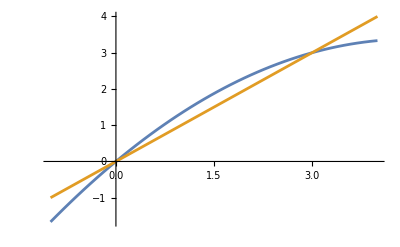

```mathematica
Plot[{f[x], g[x]}, {x, -1, 4}]
```

```mathematica
(* V točki 0 je neggibna točka, torej je za x = 0 limita zaporedja 0, za vse ostale x na (0, 3], pa je limita 3] *)
```

4. Poišči vsa realna števila , za katera konvergira vrsta 

.

```mathematica
(* Kvocientni kriterij *)
```

```mathematica
Clear[n, x]
```

```mathematica
a[n_] := Power[x, n] / (Power[x, 2n] + n)
```

```mathematica
e  =a[n + 1] / a[n]
```

(x (n+x^(2 n)))/(1+n+x^(2 (1+n)))

```mathematica
Reduce[{Abs[Limit[a[n + 1] / a[n],n -> Infinity]] < 1}, {x}, Reals] (* ni ok *)
```

x>1

```mathematica
a[n] /. {x -> 1}
```

1/(1+n)

```mathematica
a[n] /. {x -> -1}
```

(-1)^n/((-1)^(2 n)+n)

```mathematica
(* za |x| > 1 vrsta konvergira po kvocientnem kriteriju, za -1 < x < 1 brez 0 konvergira po kvocientnem kriteriju, 
za x = 0 je vsota vrste 0, za x = 1 je harmonična vrsta in divergira, za x = -1 konvergira po Leibnizevem kriteriju *)
```

## 3. kolokvij iz Matematike 1

-Graphics-

```mathematica
ClearAll[a, f, x, b]
f[x_] := Piecewise[{
{ArcTan[1/(x*x - 1)], x > 1}, 
{a, x == 1},
{(b Sin[x- 1])/ (x * x - 1), x < 1}
}]

limita1 = Limit[f[x], x -> 1, Direction->"FromAbove"]
```

π/2

```mathematica
limita2 = a
```

a

```mathematica
limita3 = Limit[f[x], x -> 1, Direction->"FromBelow"]
```

b/2

```mathematica
Solve[{limita1 == limita2 == limita3}]
```

{{a→π/2,b→π}}

-Graphics-

```mathematica
(* k tangente *)
ClearAll[x, f,a, g]
f[x_] := Sqrt[x * x + 1]
```

```mathematica
df= D[f[x], x];
kTangente = df /. {x -> 1}; (* v točki T*)
kNormale = - 1 / kTangente;
normalaT[x_] := kNormale * (x - 1) + f[1];
g[x_] := a - x*x;
```

```mathematica
dg = D[g[x], x];
xDotikalisca  = (Solve[dg == kNormale][[1]] // Values)[[1]]
```

1/(√2)

```mathematica
yg = g[xDotikalisca]
```

-1/2+a

```mathematica
normalaT[xDotikalisca]
```

√2-√2 (-1+1/(√2))

```mathematica
aR = (Solve[yg == normalaT[xDotikalisca], {a}][[1]] // Values)[[1]]
```

1/2 (-1+4 √2)

```mathematica
gg[x_] := g[x] /. {a -> aR}
```

```mathematica
Plot[{f[x], gg[x] , normalaT[x]}, {x, 0, 1.1}, PlotLabels->Automatic, AspectRatio->Automatic]
```

-Graphics-

-Graphics-

```mathematica
b[a_] := (l - a)/2
```

```mathematica
S[a_ ] := 1/2 * a * Sqrt[Power[b[a], 2] - Power[a, 2]/4]
dS = D[S[a], a]
```

```mathematica
Solve[dS == 0, {a}]
```

{{a→l/3}}

```mathematica
(* Enakostranični trikotnik s stranicami dolžine l/3 *)
```

-Graphics-

```mathematica
ClearAll[f, x]
```

```mathematica
f[x_] := (Log[x + 1])/(x+1)
```

```mathematica
(* definicijsko območje *)
FunctionDomain[f[x], x]
```

x>-1

```mathematica
(* Zaloga vrednosti *)
FunctionRange[f[x], x, y]
```

y≤1/ⅇ

```mathematica
(* Ničle *)
Reduce[f[x]==0, x]
```

x==0

```mathematica
(* Linearne asimptote *)
Limit[f[x], x-> Infinity]
```

0

```mathematica
(* Ekstremi *)
```

```mathematica
df = D[f[x], x];
Map[{#, f[#]}&, Solve[df == 0, x] // Flatten // Values]
```

{{-1+ⅇ,1/ⅇ}}

```mathematica
ddf = D[f[x], {x, 2}] ;
ddf /. {x -> -1 + E}
```

-1/ⅇ^3

```mathematica
(* V točki -1 + e je lokalni maksimum*)
```

```mathematica
(* Območja naraščanja *)
Reduce[df >= 0, x]
```

-1<x≤-1+ⅇ

```mathematica
(* Območja padanja *)
```

```mathematica
Reduce[df <= 0, x]
```

x≥-1+ⅇ

```mathematica
(* Prevoji *)
```

```mathematica
Reduce[ddf == 0, x]
```

x==-1+ⅇ^(3/2)

```mathematica
(* Konveksnost / konkavnost *)
Reduce[ddf >= 0, x] (* konveksno *)
Reduce[ddf <= 0, x] (* konkavno *)
```

x≥-1+ⅇ^(3/2)

-1<x≤-1+ⅇ^(3/2)

```mathematica
Plot[f[x], {x, -1, 4}, PlotLabels->Automatic]
```

-Graphics-